```mathematica
(*блок ввода*)
(*холестерик*)
{ϵ1 = 1,ϵ2 = 1.2,q =10, L =1};
(*траектория, заряд*)
{β3=1,Z =1,e=1};
```

```mathematica
(******************обозначения*******************)
long ={k0= √ϵ2 ko,k3 =  √(ϵ2 ko^2-kp^2), δϵ =(ϵ1 - ϵ2)/ϵ2,kp= np ko ,n3= (√(ϵ2 ko^2-kp^2))/ko,Subscript[n, 3]= (√(ko^2-kp^2))/ko};
(*ветви дисперсии*)
p31 = k3 (1+δϵ/4);(*k3 (1+δϵ/4-δϵ^2/64(4 k3^2+kp^2-2 q^2)/(k3^2-q^2));*)
p32 = k3(1+δϵ/4 k0^2/k3^2);(* k3(1+δϵ/4 k0^2/k3^2-δϵ^2/64 k0^2(4 k3^4+k3^2(3 kp^2-2 q^2)-2 kp^2)/(k3^4(k3^2-q^2)));*)
(*гармоники*)
y1[n_] := ko-β3 (p31 + 2 q n);
y2[n_] := ko-β3 (p32 + 2 q n);
yy1[n_]:= ko+β3(p31 + 2 q n);
yy2[n_]:= ko+β3(p32 + 2 q n);
(*мода1*)
ap1[n_] := 1 KroneckerDelta[n,0] + (δϵ/(16q)(2 k3^2+kp^2)/(k3+q))KroneckerDelta[n,2]+ δϵ/(16q)kp^2/(k3-q)KroneckerDelta[n,-2];
am1[n_]:= (1-(δϵ k3 k0^2)/(8q kp^2)(2 k3^2+kp^2)/(k3^2-q^2))KroneckerDelta[n,0] +(-δϵ/(16 q)kp^2/(k3+q))KroneckerDelta[n,2]+(-δϵ/(16 q)(2 k3^2+kp^2)/(k3-q))KroneckerDelta[n,-2];
(*мода2*)
ap2[n_]:= KroneckerDelta[n,0] + (-δϵ/(16q)(2 k3^2+kp^2)/(k3+q))KroneckerDelta[n,2]+ δϵ/(16q)kp^2/(k3-q)KroneckerDelta[n,-2];
am2[n_]:= (-1-(δϵ k3^3)/(8q kp^2)(2 k3^2+kp^2)/(k3^2-q^2)) KroneckerDelta[n,0] +  δϵ/(16q)kp^2/(k3+q)KroneckerDelta[n,2] +(-δϵ/(16q)(2 k3^2+kp^2)/(k3-q))KroneckerDelta[n,-2];
(*коэффициенты при модах*)
{r1= 1/(2 √2) (ϵ2 Subscript[n, 3]+n3)/ϵ2,r2 =-s (Subscript[n, 3]+n3)/n3  1/(2 √2),l1 =(ϵ2 Subscript[n, 3] - n3)/ϵ2  1/(2 √2),l2 =-s (Subscript[n, 3]-n3)/n3  1/(2 √2)};
(*нормировочный множитель *)
cSqrd =( 1/16(12+((ϵ2^2+1)(ϵ2^2 Subscript[n, 3]^4+n3^4))/(ϵ2^2 Subscript[n, 3]^2 n3^2)-Cos[p31 L]^2((ϵ2^2 Subscript[n, 3]^2-n3^2)^2)/(ϵ2^2 Subscript[n, 3]^2 n3^2)-Cos[p32 L]^2((Subscript[n, 3]^2-n3^2)^2)/(Subscript[n, 3]^2 n3^2)))^-1;
(**)
δN[x_]:= Sin[L/β3  x/2]/(π x);
```

```mathematica
(************************излучение********************)
(*ВАЖНО! сумма конечная!*)
dP = Abs[Z e β3]^2 cSqrd ( Sum[((δN[y1[n]]^2 Abs[r1]^2 KroneckerDelta[m,2n] +δN[yy1[n]]^2 Abs[l1]^2 KroneckerDelta[m,-2n])(p31+2q n)^2(ap1[ 2n]+am1[2n])^2+(δN[y2[n]]^2 Abs[r2]^2 KroneckerDelta[m,2n] +δN[yy2[n]]^2 Abs[l2]^2 KroneckerDelta[m,-2n])(p32+2q n)^2(ap2[2n]+am2[ 2n])^2),{n,-20,20}])np^5 1/(8 n3^4);
```

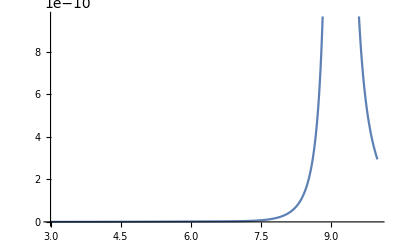

```mathematica
Plot[dP/.{s-> 1, m-> 2,np->0.1},{ko,3,10}]
```

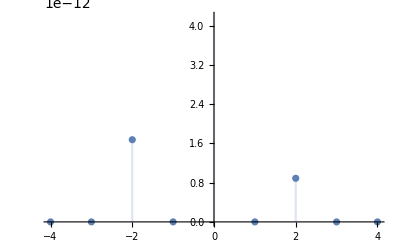

```mathematica
DiscretePlot[dP/.{s-> 1,ko-> 5,np-> 0.1},{m,-4,4}]
```